The image charges for two spherical conductor with same radius (=1) and charge ratio 7.

```mathematica
c=4;(*sphere center seperation*)
r=7;(*charge ratio:*)
V[x_,y_]:=2.759573817*((1.000000000000/((x-0.000000000000)^2+y^2)^0.5+0.066666666667/((x-0.568181818182)^2+y^2)^0.5+0.005238095238/((x-0.719870327994)^2+y^2)^0.5+0.000432167581/((x-0.788394408959)^2+y^2)^0.5+0.000036480852/((x-0.826365559403)^2+y^2)^0.5+0.000003119478/((x-0.849806493473)^2+y^2)^0.5+0.000000268903/((x-0.865253785030)^2+y^2)^0.5+0.000000023304/((x-0.875875796545)^2+y^2)^0.5+0.000000002027/((x-0.883395169832)^2+y^2)^0.5+0.000000000177/((x-0.888828330312)^2+y^2)^0.5+0.000000000015/((x-0.892812455323)^2+y^2)^0.5)-(0.250000000000/((x-3.750000000000)^2+y^2)^0.5+0.019426048565/((x-3.708609271523)^2+y^2)^0.5+0.001596917123/((x-3.695134003837)^2+y^2)^0.5+0.000134564338/((x-3.688629262949)^2+y^2)^0.5+0.000011494976/((x-3.684903848027)^2+y^2)^0.5+0.000000990250/((x-3.682559183133)^2+y^2)^0.5+0.000000085781/((x-3.680994909500)^2+y^2)^0.5+0.000000007459/((x-3.679910293293)^2+y^2)^0.5+0.000000000650/((x-3.679138018936)^2+y^2)^0.5+0.000000000057/((x-3.678577685139)^2+y^2)^0.5+0.000000000005/((x-3.678165548226)^2+y^2)^0.5))+7.225364963*((1.000000000000/((x-4.000000000000)^2+y^2)^0.5+0.066666666667/((x-3.431818181818)^2+y^2)^0.5+0.005238095238/((x-3.280129672006)^2+y^2)^0.5+0.000432167581/((x-3.211605591041)^2+y^2)^0.5+0.000036480852/((x-3.173634440597)^2+y^2)^0.5+0.000003119478/((x-3.150193506527)^2+y^2)^0.5+0.000000268903/((x-3.134746214970)^2+y^2)^0.5+0.000000023304/((x-3.124124203455)^2+y^2)^0.5+0.000000002027/((x-3.116604830168)^2+y^2)^0.5+0.000000000177/((x-3.111171669688)^2+y^2)^0.5+0.000000000015/((x-3.107187544677)^2+y^2)^0.5)-(0.250000000000/((x-0.250000000000)^2+y^2)^0.5+0.019426048565/((x-0.291390728477)^2+y^2)^0.5+0.001596917123/((x-0.304865996163)^2+y^2)^0.5+0.000134564338/((x-0.311370737051)^2+y^2)^0.5+0.000011494976/((x-0.315096151973)^2+y^2)^0.5+0.000000990250/((x-0.317440816867)^2+y^2)^0.5+0.000000085781/((x-0.319005090500)^2+y^2)^0.5+0.000000007459/((x-0.320089706707)^2+y^2)^0.5+0.000000000650/((x-0.320861981064)^2+y^2)^0.5+0.000000000057/((x-0.321422314861)^2+y^2)^0.5+0.000000000005/((x-0.321834451774)^2+y^2)^0.5));
Ex=-D[V[x,y],x];
Ey=-D[V[x,y],y];
```

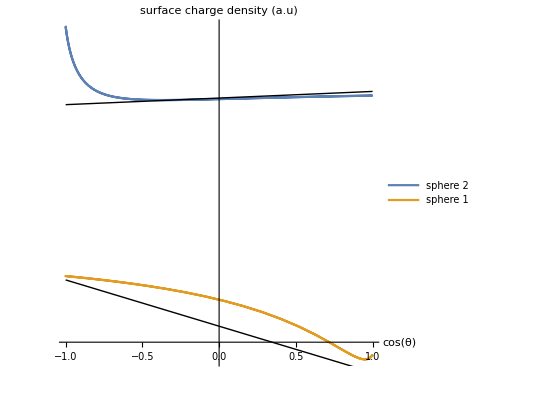

```mathematica
Show[ParametricPlot[{{Cos[θ],Ey Sin[θ]+Ex Cos[θ]}/.{x->c+Cos[θ],y->Sin[θ]},{Cos[θ],Ey Sin[θ]+Ex Cos[θ]}/.{x->Cos[θ],y->Sin[θ]}},
{θ,0,2 Pi},PlotLegends->{"sphere 2","sphere 1"},AxesLabel->{Cos[θ],"surface charge density (a.u)"},Ticks-> {Automatic,None}],
(*Lekner approximation:*)
Graphics[Line[{{-1,1+3r/c^2-5r/c^3},{1,1-3r/c^2-5r/c^3}}]],Graphics[Line[{{-1,r-3/c^2-5/c^3},{1,r+3/c^2-5/c^3}}]],AspectRatio-> 1]
```

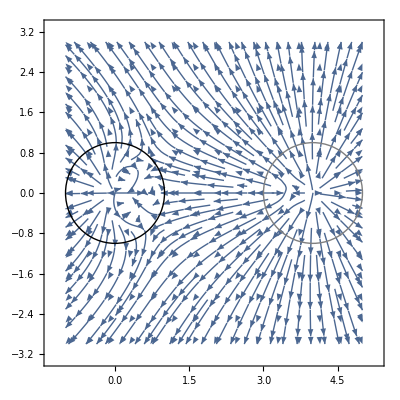

```mathematica
Show[VectorPlot[{Ex,Ey},{x,-1,c+1},{y,-3,3},StreamPoints-> Fine],Graphics[{Thick,Black,Circle[{0,0},1]}],Graphics[{Thick,Gray,Circle[{c,0},1]}]]
```